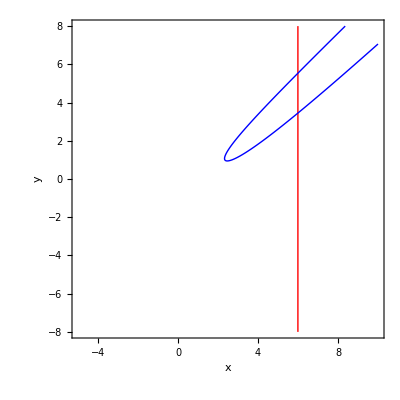

{x→5.99519,y→3.44976}

{x→5.99519,y→5.5364}

```mathematica
f[x_, y_]:=(x-1)^(2/3)+(x-3)^(2/3)-5
g[x_, y_]:=Sqrt[x^2-y^2]-2Cosh[x-y-1]

ContourPlot[{f[x, y]==0, g[x, y]==0}, {x, -5, 10}, {y, -8, 8},
ContourStyle->{{Red, Thick}, {Blue, Thick}},
FrameLabel->{"x", "y"},
PlotPoints->100,
MaxRecursion->4]

sol1 = FindRoot[{f[x, y]==0, g[x, y]==0}, {{x, 6.3}, {y, 0}}]
sol2 =  FindRoot[{f[x, y]==0, g[x, y]==0}, {{x, 3.7}, {y, 2.6}}]
```